# Math 223: Homework 7

<Zihan Xu>

<3/22/2023>

## Problem 1

#### Find the first two terms of the asymptotic expansion of

∫_5^9 ⅇ^(-x t)/t ⅆt,  x->+∞.

Solution:

Let us apply integration by parts with u=f(t)=1/t and ⅆv=ⅇ^(-x t)ⅆt. This yields,

I(x) = -1/(x t)ⅇ^(-x t)|_5^9+1/x∫_5^9 ((- 1)/t^2)ⅇ^(-x t)ⅆt
         = 1/(5x)ⅇ^(-5x)-1/(9x)ⅇ^(-9x)-1/x∫_5^9 ⅇ^(-x t)/t^2 ⅆt
         = ∑_(n=0)^(m-1) ⅇ^(-5x)/(5x)^(n+1)(-1)^n-∑_(n=0)^(m-1) ⅇ^(-9x)/(9x)^(n+1)(-1)^n+1/x^m∫_5^9 (-1)^m t^(-m-1) ⅇ^(-x t)ⅆt

Since ⅇ^(-9x)<< ⅇ^(-5x) as x->+∞, we can neglect the second sum and rewrite it as 
I(x) ∼∑_(n=0)^(m-1) ⅇ^(-5x)/(5x)^(n+1)(-1)^n+1/x^m∫_5^9 (-1)^m t^(-m-1) ⅇ^(-x t)ⅆt.

f^(m)(t) is continuous on [5,9] for all positive integer m. To get the first two terms, we can write it as
I(x) ∼∑_(n=0)^1 ⅇ^(-5x)/(5x)^(n+1)(-1)^n+1/x^2∫_5^9 t^-3 ⅇ^(-x t)ⅆt =  ⅇ^(-5x)/(5x)-ⅇ^(-5x)/(25 x^2)+O(x^-3) as x->∞
Therefore, the first two terms of the asymptotic expansion is   ⅇ^(-5x)/(5x)-ⅇ^(-5x)/(25 x^2), x-> +∞.

```mathematica
AsymptoticIntegrate[ⅇ^(-x t)/t,{t,5,9},{x,∞,2}]
```

(2 ⅇ^(-5 x))/(125 x^3)-ⅇ^(-5 x)/(25 x^2)+ⅇ^(-5 x)/(5 x)

```mathematica
ExactIntegral1[x_] = Integrate[ⅇ^(-x t)/t,{t,5,9},Assumptions->x>0]
```

ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x]

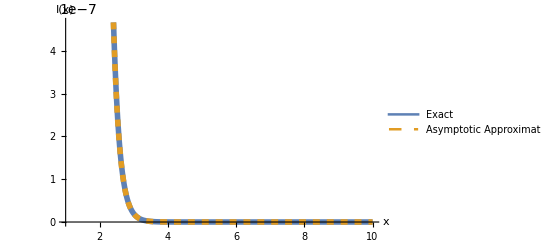

```mathematica
Plot[{ExactIntegral1[x],  ⅇ^(-5x)/(5x)-ⅇ^(-5x)/(25 x^2)},{x,1,10},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Asymptotic Approximation"}]
```

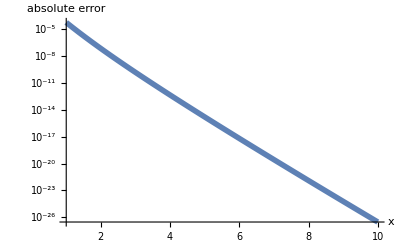

```mathematica
LogPlot[Abs[ExactIntegral1[x]-(ⅇ^(-5x)/(5x)-ⅇ^(-5x)/(25 x^2))],{x,1,10},
PlotStyle-> Directive[Solid,Thickness[0.01]],AxesLabel->{Style["x",Italic,18],Style["absolute error", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 2

Use Watson’s lemma to determine the asymptotic expansion of

I(x)=∫_0^π ⅇ^(-x t) t^(-1/3)cos tⅆt,  x->+∞.

Solution:

f(t)=t^(-1/3)cos t is integrable on [0,π]. Consider a parameter 0<R<π, and write  I(x)= ∫_0^R ⅇ^(-x t)t^(-1/3)cos tⅆt+∫_R^π ⅇ^(-x t)t^(-1/3)cos tⅆt.

Let’s consider the second integral. Since the upper bound is π, we can bound f(t) by a constant, |t^(-1/3)|<= R^(-1/3) and |cos t|<=1, as t∈ [R,π], and then find
|∫_R^π ⅇ^(-x t)t^(-1/3)cos t  ⅆt |<= R^(-1/3)∫_R^π ⅇ^(-x t)ⅆt = R^(-1/3)/x(ⅇ^(-R x)-ⅇ^(-π x)) ∼ ⅇ^(-R x)/x, x-> +∞.

To compute the first integral,  ∫_0^R ⅇ^(-x t)t^(-1/3)cos tⅆt=∫_0^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt - ∫_R^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt .

To solve for ∫_0^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt, we can use the expansion

cos t∼∑_(n=0)^∞ (-1)^n t^(2n)/((2n)!),   t→0^+,

and find

∫_0^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt ~∫_0^∞ ⅇ^(-x t)∑_(n=0)^∞ (-1)^n t^(2n-1/3)/((2n)!)ⅆt =∑_(n=0)^∞ (-1)^n/((2n)!)∫_0^∞ t^(2n-1/3)ⅇ^(-x t)ⅆt,   x→+∞.

Next, according to the definition of the Gamma function, Γ(z) = ∫_0^∞ x^(z-1)ⅇ^-x ⅆx, we can find

∫_0^∞ t^(2n-1/3)ⅇ^(-x t) ⅆt =(Γ(2/3+2n))/x^(2/3+2n),

and we find

∫_0^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt ∼∑_(n=0)^∞ (-1)^n/((2n)!)(Γ(2/3+2n))/x^(2/3+2n),   x→+∞.

From the analysis we have used for ∫_R^π ⅇ^(-x t)t^(-1/3)cos tⅆt, we can find ∫_R^∞ ⅇ^(-x t)t^(-1/3)cos tⅆt ∼ ⅇ^(-R x)/x, x-> +∞.

I(x)= ∫_0^R ⅇ^(-x t)t^(-1/3)cos tⅆt+∫_R^π ⅇ^(-x t)t^(-1/3)cos tⅆt ∼ ∑_(n=0)^∞ (-1)^n/((2n)!)(Γ(2/3+2n))/x^(2/3+2n)-ⅇ^(-R x)/x+ⅇ^(-R x)/x=∑_(n=0)^∞ (-1)^n/((2n)!)(Γ(2/3+2n))/x^(2/3+2n), x-> +∞.
Thus, we have the asymptotic expansion is ∑_(n=0)^∞ (-1)^n/((2n)!)(Γ(2/3+2n))/x^(2/3+2n), x-> +∞.

```mathematica
ExactIntegral2[x_] = Integrate[ⅇ^(-x t) t^(-1/3)Cos[t],{t,0,π},Assumptions->x>0]
```

1/2 (-π^(2/3) (ExpIntegralE[1/3,π (-ⅈ+x)]+ExpIntegralE[1/3,π (ⅈ+x)])+(1/(-ⅈ+x)^(2/3)+1/(ⅈ+x)^(2/3)) Gamma[2/3])

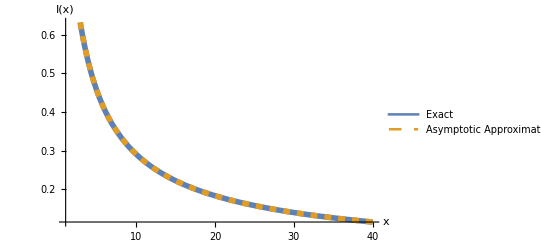

```mathematica
Plot[{ExactIntegral2[x],  Sum[(-1)^n/((2n)!)Gamma[2/3+2n]/x^(2n+2/3),{n,0,2}]},{x,1,40},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Asymptotic Approximation"}]
```

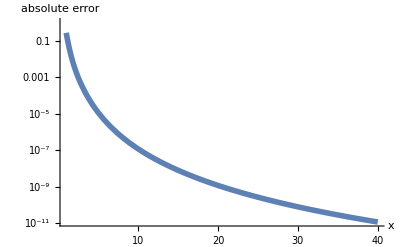

```mathematica
LogPlot[Abs[ExactIntegral2[x]-  Sum[(-1)^n/((2n)!)Gamma[2/3+2n]/x^(2n+2/3),{n,0,2}]],{x,1,40},
PlotStyle-> Directive[Solid,Thickness[0.01]],AxesLabel->{Style["x",Italic,18],Style["absolute error", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 3

#### Use Laplace’s method to determine the leading behavior of

I(x)=∫_(-1/2)^(1/2) ⅇ^(-x sin^4 t) ⅆt,  x->+∞.

Solution:

Consider the general form of a Laplace integral, I(x) = ∫_a^b f(t)ⅇ^(-x ϕ(t))ⅆt,   x→+∞. We have f(t) = 1 and ϕ(t) = Sin^4[t].
The function ϕ(t) has a local minimum at an interior point c= 0 satisfying -1/2 < c < 1/2, so that ϕ'(c) = 0 and ϕ''(c)=0.

We won’t be able to directly use the result of Laplace’s method, but we can follow the method by expanding about t=0, we find

```mathematica
ϕ = Series[Sin[t]^4,{t,0,4}]
```

t^4+O[t]^5

Thus, we find that

I(x) ∼  ∫_(-∞)^∞ ⅇ^(-x t^4)ⅆt ,   x→+∞.

Let s=x^(1/4) t, ∫_(-∞)^∞ ⅇ^(-x t^4)ⅆt = 1/x^(1/4)∫_(-∞)^∞ ⅇ^(-s^4)ⅆs,  and we can get ∫_(-∞)^∞ ⅇ^(-s^4)ⅆt = 2Gamma[5/4].

```mathematica
Integrate[ⅇ^(-s^4),{s,-∞,∞}]
```

2 Gamma[5/4]

Thus, the leading behavior is I(x) ∼ (2Gamma[5/4])/x^(1/4),   x→+∞.

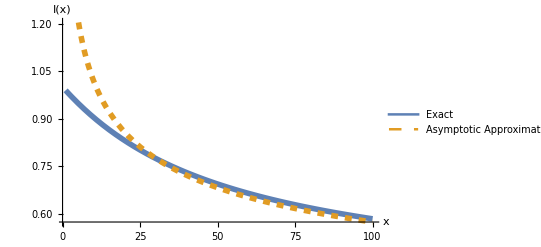

```mathematica
Plot[{NIntegrate[ⅇ^(-x Sin[t]^4),{t,-1/2,1/2}], (2Gamma[5/4])/x^(1/4)},{x,1,100},
PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Asymptotic Approximation"}]
```

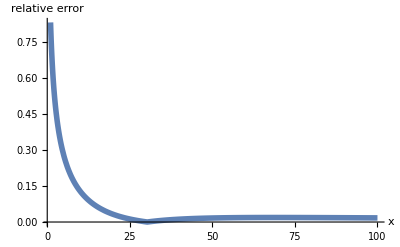

```mathematica
Plot[Abs[NIntegrate[ⅇ^(-x Sin[t]^4),{t,-1/2,1/2}]-(2Gamma[5/4])/x^(1/4)]/Abs[NIntegrate[ⅇ^(-x Sin[t]^4),{t,-1/2,1/2}]],{x,1,100},
PlotRange->All,PlotStyle-> Directive[Solid,Thickness[0.01]],AxesLabel->{Style["x",Italic,18],Style["relative error", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

## Problem 4

#### The L_p norm of a function 𝑔 is given by ∥𝑔∥_p = (I(p))^(1/p) where

I(p)=∫_a^b |𝑔(𝑡)|^p ⅆt.

Assuming that |𝑔(𝑡)|∈ C^4 and that it attains its unique maximum on t=c inside [a,b] with g(c) ≠ 0, use Laplace’s method to show that the L_p norm converges to the “maximum” norm as p->∞.

Solution:

((∥𝑔∥_p))^p = ∫_a^b |𝑔(t)|^p ⅆt = ∫_a^b ⅇ^(p log(|𝑔(t)|))ⅆt

ϕ(t)=-log(𝑔(t)), ϕ' (t) = (-𝑔'(t))/(𝑔(t)) and ϕ'' (t) = (-𝑔(t) 𝑔''(t)+𝑔'(t)^2)/(𝑔(t))^2

The function ϕ(t) has a local minimum at an interior point c satisfying a < c < b, so that ϕ'(c) = 0 and ϕ''(c)=(-𝑔''(c))/(𝑔(c)).
Using Laplace’s method, we have

((∥𝑔∥_p))^p ∼ √((2 π)/(p ϕ''(c)))ⅇ^(-p ϕ(c))=√((2 π)/(p ϕ''(c)))ⅇ^(-p ϕ(c))=√((-2 π𝑔(c))/(p 𝑔''(c)))(𝑔(c))^p,   p→+∞

Taking the power 1/p, we can get:

∥𝑔∥_p ∼ ((-2 π𝑔(c))/(p 𝑔''(c)))^(1/2p)𝑔(c),   p→+∞

where ((-2 π𝑔(c))/(p 𝑔''(c)))^(1/2p)=exp(1/(2p)[log((-2 π𝑔(c))/(𝑔''(c)))-log(p)])

We can follow the method by expanding exponential function about u=0, we find

```mathematica
Series[E^u,{u,0,1}]
```

1+u+O[u]^2

Consider u=1/(2p)[log((-2 π𝑔(c))/(𝑔''(c)))-log(p)], we can get

((-2 π𝑔(c))/(p 𝑔''(c)))^(1/2p) ∼ 1+1/(2p)[log((-2 π𝑔(c))/(𝑔''(c)))-log(p)]+O(1/p^2),   p→+∞

∥𝑔∥_p ∼ 𝑔(c)(1+1/(2p)[log((-2 π𝑔(c))/(𝑔''(c)))-log(p)]),   p→+∞

We must have 1/(2p)[log((-2 π𝑔(c))/(𝑔''(c)))-log(p)] << 1  as p→+∞ because of following:

```mathematica
Limit[(Log[(-2 π𝑔(c))/(𝑔''(c))]-Log[p])/(2p),p->∞]
```

0

Therefore, ∥𝑔∥_p ∼𝑔(c) as p->∞. Since ϕ(t)=-log(𝑔(t)) has a local minimum at an interior point c satisfying a < c < b, we must have 𝑔(t) has a local maximum at c. In other words, 𝑔(c) is the maximum norm of function g.

Hence, the L_p norm ∥𝑔∥_p ∼ 𝑔(c), where 𝑔(c) is the maximum norm of function g on [a,b], as p->∞.

## Problem 5

#### Show that

∫_0^∞ log(u/(1-e^-u))  ⅇ^(-k u)/u ⅆu ∼ 1/(2k),    k->∞.

Solution:

We can write the integral as following:

∫_0^∞ log(u/(1-ⅇ^-u))ⅇ^(-k u)/u ⅆu = ∫_0^∞ [log(u)-log(1-ⅇ^-u)]/u ⅇ^(-k u)ⅆu

We can apply Watson’s lemma where f(u)= [log(u)-log(1-ⅇ^-u)]/u. f(u) is integrable on [0, ∞). 
Consider a parameter 0<R<π, and write  ∫_0^∞ log(u/(1-ⅇ^-u))ⅇ^(-k u)/u ⅆu= ∫_0^R f(u) ⅇ^(-k u)ⅆu + ∫_R^∞ f(u) ⅇ^(-k u)ⅆu.

To evaluate the second integral ∫_R^∞ f(u) ⅇ^(-k u)ⅆu, we need to find the upper bound of f(u). Let’s take its first derivative

```mathematica
D[(Log[u]-Log[1-ⅇ^-u])/u,u]
```

(-ⅇ^-u/(1-ⅇ^-u)+1/u)/u-(-Log[1-ⅇ^-u]+Log[u])/u^2

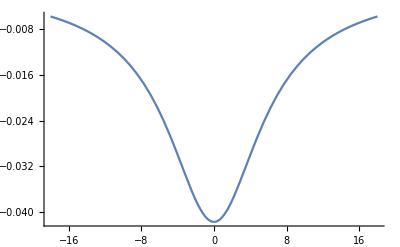

```mathematica
Plot[(-ⅇ^-u/(1-ⅇ^-u)+1/u)/u-(-Log[1-ⅇ^-u]+Log[u])/u^2,{u,-18.,18.}]
```

```mathematica
Limit[(-ⅇ^-u/(1-ⅇ^-u)+1/u)/u-(-Log[1-ⅇ^-u]+Log[u])/u^2,u->∞]
```

0

We can observe that f'(u)<0, ∀ u>=0, so f(u) is a monotonically decreasing function.

We can find its upper bound by taking limit:

```mathematica
Limit[(Log[u]-Log[1-ⅇ^-u])/u,u->0, Direction->"FromAbove"]
```

1/2

We can conclude that |f(u)|≤ 1/2, and then we find that

|∫_R^∞ f(u)ⅇ^(-k u)ⅆu|≤ ∫_R^∞ 1/2 ⅇ^(-k u)ⅆu=1/2 ⅇ^(-k R)/k∼ ⅇ^(-k R)/k,   k→+∞.

To compute the first integral ∫_0^R f(u) ⅇ^(-k u)ⅆu. We assume f(u) has the following asymptotic expansion,

```mathematica
Series[(Log[u]-Log[1-ⅇ^-u])/u,{u,0,0}]
```

1/2+O[u]^1

By substituting this asymptotic expansion into the integral, we find

∫_0^R f(u)ⅇ^(-k u)ⅆt∼∫_0^R (1/2)ⅇ^(-k u)ⅆu,   k→+∞.

Next, we write

∫_0^R (1/2)ⅇ^(-k u)ⅆu=∫_0^∞ 1/2 ⅇ^(-k u)ⅆu-∫_R^∞ 1/2 ⅇ^(-k u)ⅆu.

We can get ∫_0^∞ 1/2 ⅇ^(-k u)ⅆu = 1/(2k).

```mathematica
Integrate[1/2 ⅇ^(-k u),{u,0,∞}, Assumptions->k>0]
```

1/(2 k)

From the analysis we have used above, we can find that

∫_R^∞ 1/2 ⅇ^(-k u)ⅆu∼ ⅇ^(-k R)/k,   k→+∞.

∫_0^∞ log(u/(1-ⅇ^-u))ⅇ^(-k u)/u ⅆu ∼ 1/(2k) - ⅇ^(-k R)/k + ⅇ^(-k R)/k = 1/(2k), k->+∞.

Hence, we can get ∫_0^∞ log(u/(1-ⅇ^-u))ⅇ^(-k u)/u ⅆu ∼1/(2k), k->+∞.